# μLang — Computationally Generating a Morphologically Average Conlang Lexicon from Multilingual Translations

Constructed languages, or conlangs, are languages that were artificially created instead of being naturally evolved over several generations. A crucial part of every conlang is the lexicon — the vocabulary. While most conlang lexicons are generated manually or through the help of randomized selection, I present several methods to generating a quantitatively “average” lexicon, that is, generating new words that may have similar features, spelling, or pronunciation compared to several translations of the same word in different languages.

## Initial Setup

I start with a simple word and and use translations provided by the Wolfram Language. In this case, I’m using “water”.

```mathematica
KEYWORD = "water";
```

Get the top 25 most spoken languages:

```mathematica
languages=EntityClass["Language",{"TotalSpeakers"->TakeLargest[100]}]//EntityList;
Iconize[languages, "List of languages"]
```

Get raw translations of our keyword to the determined languages:

```mathematica
rawTranslations = KeyValueMap[#1->First[#2]&,WordTranslation[KEYWORD, languages]];
rawTranslations//Short
```

{Chinese→卑鄙的,English→mean,Mandarin Chinese→卑鄙的,Hindi→कृपण,Arabic→حَقير,Spanish→mordaz,French→caustique,Standard Arabic→NotAvailable,Bengali→নীচ,Russian→средний,«80»,Southern Pashto→NotAvailable,Chhattisgarhi→NotAvailable,Rajasthani→NotAvailable,Cebuano→bangis,Mesopotamian Arabic→NotAvailable,Nigerian Fulfulde→NotAvailable,Assamese→অধম,Northeastern Thai→NotAvailable,Zhuang→NotAvailable,Northern Kurdish→NotAvailable}

Standardize all translated words — Transliterate to the Roman alphabet for easier string manipulation, ensure all words are lowercase, and remove translations that are not available.

```mathematica
translatedList=DeleteCases[DeleteDuplicates[ToLowerCase[Select[Transliterate[Values[rawTranslations]],StringMatchQ[#,CharacterRange["A","z"]..]&]]], "notavailable"]
```

{mean,krpana,haqyr,mordaz,caustique,nica,srednij,jahat,bkhyl,schnippig,bayagi,mattamana,mugu,secco,kanjusa,sankinrnamana,nikczemny,adhamanaya,fai,kamina,kmynh,pidlij,adna,hamak,ticalos,dinahina,kattig,nabuntu,kedekut,gemeen,bangis,adhama}

As a visual, I compared the edit distance between all pairs of multilingual words.

Compare the distance between every pair of words:

```mathematica
visualizeDistanceMatrix[wordList_]:=Module[{matrix,n},
n=Length[wordList];
matrix=Table[
EditDistance[wordList[[i]],wordList[[j]]],
{i,n},
{j,n}
];
ArrayPlot[matrix,ColorFunction->"Rainbow",PlotLabel->"Word Distance Matrix",ImageSize->{1200, 1200},FrameLabel->{"Words","Words"},PlotLegends->Automatic,FrameTicks->{Table[{i,wordList[[i]]},{i,n}],Table[{i,wordList[[i]]},{i,n}]}]]
```

Plot and visualize the distance matrix:

```mathematica
visualizeDistanceMatrix[translatedList]
```

-Graphics-

## Most Common Letter

Naturally, this is the very first idea I jumped to. I counted the most frequent letter at every index, found the average length of the original words, and concatenated the most common letters together.

Split each word into a List of characters:

```mathematica
charLists = Characters /@ translatedList;
charLists//Short
```

{{m,e,a,n},{k,r,p,a,n,a},{h,a,q,y,r},{m,o,r,d,a,z},«1»,{«1»},{«1»},{j,a,h,a,t},{b,k,h,y,l},{s,c,h,n,i,p,p,i,g},{b,a,y,a,g,i},{m,a,t,t,a,m,a,n,a}}

Find the average length of all words:

```mathematica
avgLen=Round[Mean[Length/@charLists]]
```

6

For words shorter in length than the average length, pad the List with dashes. For words longer than the average length, truncate the List accordingly:

```mathematica
augmentedLists=
Map[
Function[chars,
If[Length[chars]>avgLen,
Take[chars,avgLen],
PadRight[chars,avgLen,"-"]
]
],charLists];

augmentedLists//Short
```

{{m,e,a,n,-,-},{k,r,p,a,n,a},{h,a,q,y,r,-},{m,o,r,d,a,z},{c,a,u,s,t,i},{«1»},«1»,{j,«4»,-},{b,k,h,y,l,-},{s,c,h,n,i,p},{b,a,y,a,g,i},{m,a,t,t,a,m}}

Transpose the charList for easier calculation of the most frequent character at every position:

```mathematica
transposed=Transpose[augmentedLists];
```

Find the most frequency character at each position and generate the average word:

```mathematica
mostFreqChar=
Map[
If[
DeleteCases[#,"-"]==={},
"-",
First@First@SortBy[Tally@DeleteCases[#,"-"],-Last[#]&]]&,
transposed
];
```

```mathematica
mostFreqCharWord=StringJoin[DeleteCases[mostFreqChar,"-"]]
```

mahaai

While this method does “work,” it is rather boring. It always produces one very predictable word and isn’t very creative. To generate an exciting lexicon, I explored some other methods.

## Most Common Digram

My second approach was to split each word into digrams (pairs of consecutive letters) and find the most common digram in each position. Then, we can join the most common digrams together. For example, “su” is the first digram in “sun” and “un” is the second digram in “sun.”

Calculate the average syllable count:

```mathematica
SYLLABLECOUNT = Round[Mean[Length/@(ResourceFunction["WordSyllables"][#]&/@translatedList)]]
```

2

Split each word into digrams and record the position of each digram:

```mathematica
positionedDigrams=Flatten[
Table[
If[
StringLength[word]>=pos+1,
{pos,StringTake[word,{pos,pos+1}]},
Nothing],
{word,translatedList},
{pos,StringLength[word]-1}
],1];
positionedDigrams//Short
```

{{1,me},{2,ea},{3,an},{1,kr},{2,rp},{3,pa},{4,an},{5,na},{1,ha},{2,aq},{3,qy},{4,yr},{1,mo},{2,or},«35»,{8,ig},{1,ba},{2,ay},{3,ya},{4,ag},{5,gi},{1,ma},{2,at},{3,tt},{4,ta},{5,am},{6,ma},{7,an},{8,na}}

Group digrams by their position:

```mathematica
groupedByPosition=GroupBy[positionedDigrams,First->Last];
Iconize[groupedByPosition]
```

Count the frequency of each digram in each position:

```mathematica
countsByPosition=AssociationMap[Counts[groupedByPosition[#]]&,Keys[groupedByPosition]];
countsByPosition//First
```

<|me→1,kr→1,ha→1,mo→1,ca→1,ni→1,sr→1,ja→1,bk→1,sc→1,ba→1,ma→1|>

Get the most frequent digram in each position:

```mathematica
topDigramsByPosition=Table[Keys@TakeLargestBy[countsByPosition[pos],Identity,UpTo[1]],{pos,Sort@Keys[countsByPosition]}]
```

{{me},{ea},{an},{an},{na},{iq},{qu},{ue}}

Generate new words by combining the most frequent digrams:

```mathematica
generateWord[]:=Module[{numSyllables,selectedLists,syllables},
numSyllables:=RandomInteger[{Max[1, SYLLABLECOUNT-2], Min[Length[topDigramsByPosition], SYLLABLECOUNT+2]}];
selectedLists=Take[topDigramsByPosition,numSyllables];
syllables=RandomChoice/@selectedLists;
StringJoin[syllables]
]
```

Generate the most

```mathematica
mostDigramGenerated=DeleteDuplicates[Table[generateWord[],{10}]]
```

{me,meea,meeaan,meeaanan}

This isn’t great either. While there are some pronounceable words, this method is very basic and relies on the most common digrams. In fact, both of the previous methods relied very strictly on the most frequent characters with extremely basic substitution algorithms.

## Genetic Evolution

A different approach is to imagine the original list of translated words as a base “population.” Through a genetic algorithm, we can “evolve” the population and generate new words that are similar but completely unique.

Define important variables. populationSize is the size of the population each generation and mutationRate:

```mathematica
Clear[populationSize, generations, mutationRate, topDigramsByPosition, fitnessFunction, population, randomString, allBest];
populationSize=100;
generations=100;
mutationRate=0.2;
topDigramsByPosition=Table[Keys@TakeLargestBy[countsByPosition[pos],Identity,UpTo[5]],{pos,Sort@Keys[countsByPosition]}]
allBest = {};
words = translatedList;
charSet = Flatten[topDigramsByPosition];
MAXLENGTH = Round[Mean[StringLength/@ words]]
allPopulations = {};
avgFitnessPerGen = {};
```

{{me,kr,ha,mo,ca},{ea,rp,aq,or,au},{an,pa,qy,rd,us},{an,yr,da,st,dn},{na,az,ti,ni,ip},{iq,ij,pp,ma},{qu,pi,an},{ue,ig,na}}

6

```mathematica
phoneticDifference[word1_String,word2_String]:=Module[{soundex1,soundex2},
soundex1=ResourceFunction["Soundex"][word1];
soundex2=ResourceFunction["Soundex"][word2];
If[soundex1===soundex2,0,EditDistance[soundex1,soundex2]]]
```

Our fitness function will calculate the average Levenshtein distance between a candidate word and each word in the original word list:

```mathematica
(*fitnessFunction[candidate_String]:=Module[{maxDistance},maxDistance=Max[EditDistance[candidate,#]&/@words];
1-N[Mean[EditDistance[candidate,#]&/@words]/maxDistance]]*)

fitnessFunction[candidate_String]:=Module[{maxEditDistance,maxPhoneticDistance,editScore,phoneticScore},(*Calculate maximum edit distance*)maxEditDistance=Max[EditDistance[candidate,#]&/@words];
(*Calculate maximum phonetic distance*)maxPhoneticDistance=Max[phoneticDifference[candidate,#]&/@words];
(*Calculate normalized edit distance score (0 to 1)*)editScore=If[maxEditDistance>0,1-N[Mean[EditDistance[candidate,#]&/@words]/maxEditDistance],1];
(*Calculate normalized phonetic distance score (0 to 1)*)phoneticScore=If[maxPhoneticDistance>0,1-N[Mean[phoneticDifference[candidate,#]&/@words]/maxPhoneticDistance],1];
(*Combine scores with 50% weighting each*)0.5*editScore+0.5*phoneticScore]
```

The fitness of a word similar to possible KEYWORD translations is significantly greater than a completely unrelated fitness word:

```mathematica
fitnessFunction[WordTranslation[KEYWORD, "Spanish"][[1]]]
```

0.310185

```mathematica
fitnessFunction["random word"]
```

0.132576

Here is our list of possible digrams:

```mathematica
charSet
```

{me,kr,ha,mo,ca,ea,rp,aq,or,au,an,pa,qy,rd,us,an,yr,da,st,dn,na,az,ti,ni,ip,iq,ij,pp,ma,qu,pi,an,ue,ig,na}

Create our original population by randomly combining digrams:

```mathematica
randomString[]:=StringJoin@RandomChoice[Flatten[topDigramsByPosition],RandomInteger[{SYLLABLECOUNT,SYLLABLECOUNT+2}]];
population=Table[randomString[],{populationSize}];
population
```

{dnnapior,dnrpca,usnihast,mequ,orij,rdanrp,nitiuean,iqaqan,anaqippi,orppst,pana,anpi,rppi,rpyr,caea,anyr,meppau,modana,modacaau,medana,tina,caanus,yrue,aquenini,haij,qyaz,dndnanha,dausdnha,auyrpime,anau,rdueme,qumeau,qupa,azanme,mardma,ororanda,nardtida,quni,hanaipan,picapiea,moquigan,uetian,maqy,morpiqti,dnanma,yrkr,dnazqyig,aqna,ueiporca,daip,meiq,cast,anijrpti,meiqiqna,cadaniaz,uerp,naijha,rddaus,usrpig,anyrti,iqmetime,meanpp,maan,orni,quiq,orrp,caij,caijpp,anpa,rdananpi,ipor,iqstna,krpp,ipaqazmo,naha,naanig,qunaij,rpppni,ustipp,anigrd,iqtiijan,iphard,niusqy,piqumo,mastqu,ijipcaan,niha,mepa,cana,paniti,rpauti,eadnrpaz,stau,usuenina,ppqyor,naqumequ,piandnqu,meor,nimoue,rpig}

With everything set up, I can simulate several hundred generations of evolution. I used a modified two-point crossover algorithm that allowed both parent words to vary in length.

Implementation of crossover:

```mathematica
lengthVaryTwoPointCrossover[p1_,p2_]:=Module[{len1,len2,minLen,pt1,pt2,c1,c2,child},
len1=StringLength[p1];
len2=StringLength[p2];
minLen=Min[len1,len2];
{pt1,pt2}=Sort@RandomSample[Range[minLen],2];
c1=Characters[p1];
c2=Characters[p2];
child=Join[Take[c1,pt1-1],Take[c2,{pt1,pt2}],Drop[c1,pt2]];
If[
Length[child]>
MAXLENGTH,
child=Take[child,MAXLENGTH]
];
StringJoin[child]];
```

Implementation of string mutation:

```mathematica
mutate[str_]:=StringJoin@
Table[
If[RandomReal[]<mutationRate,
RandomChoice[charSet],
c
],
{c,Characters[str]}
];
```

I record the best/”most fit” word each generation:

```mathematica
allBest=Table[fitnesses=fitnessFunction/@population;
bestCandidate=population[[First@Ordering[fitnesses,-1]]];
avgF=N[Mean[fitnesses]];
AppendTo[avgFitnessPerGen,avgF];
AppendTo[allPopulations,population];
parents=TakeLargestBy[Transpose[{population,fitnesses}],Last,Ceiling[populationSize/2]][[All,1]];
population=Table[mutate@lengthVaryTwoPointCrossover[RandomChoice[parents],RandomChoice[parents]],{populationSize}];
bestCandidate,{gen,1,generations}];

AppendTo[allPopulations,population];
```

The best performing strings in each generation:

```mathematica
allBest//Short
```

{maqy,maiq,masau,mhaan,mquaa,musau,maaaaz,miaqa,mmoqaa,mstaaa,maaraa,maataa,mnja,maja,msea,«70»,mueaqy,mueaqy,maqyan,maqyae,maakaa,maqaaea,muaeeq,mmazau,masuau,muaaqa,maayzq,mktaaa,moyqaa,mqaday,moyqae}

Log the most fit string:

```mathematica
bestWordGeneticPool=First@MaximalBy[allBest,fitnessFunction];
Print["Best word found: ",bestWordGeneticPool];
Print["Fitness: ",fitnessFunction[bestWordGeneticPool]];
```

Best word found: masau

Fitness: 0.409722

Plot the average fitness of every population of each generation over time:

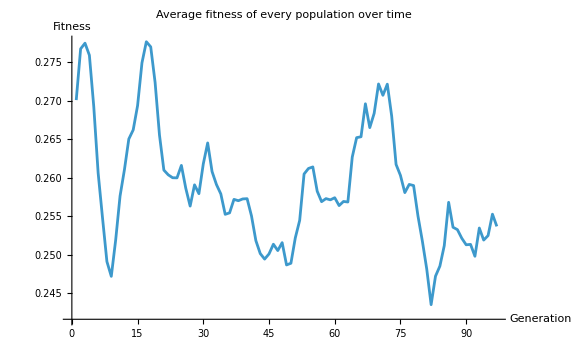

```mathematica
ListLinePlot[MovingAverage[avgFitnessPerGen,4],ImageSize->Large,PlotLabel->"Average fitness of every population over time",AxesLabel->{"Generation","Fitness"}]
```

Overall, there is a trend of increasing fitness throughout the graph. There are many fluctuations due to rando

## String Optimization

Linguistic evolution can also be viewed as an optimization problem. I want to continuously evolve a string to be have the lowest average edit distance to all the multilingual words. I take a string and evolve it through several hundred generations. Each generation, I evolve the string towards the multilingual word that is most different from it.

Set up basic variables:

```mathematica
Clear[baseWord, testList, padChar, baseWordStates, targetWords,GENERATIONS];
baseWord=StringJoin@RandomChoice[CharacterRange["a", "z"], 5];
startingWord = baseWord;
testList=translatedList
padChar="_";
baseWordStates={baseWord};
targetWords={};
GENERATIONS=400;
averageLength=Round[Mean[StringLength /@ testList]];

getAllChars[wordList_]:=Module[{maxLen,paddedWords,allChars},
maxLen=Max[StringLength/@wordList];
paddedWords=StringPadRight[#,maxLen,padChar]&/@wordList;
allChars=Union[Flatten[Characters/@paddedWords]];
allChars
];

pad[w1_,w2_]:=Module[{maxLen,p1,p2},
maxLen=Max[StringLength[w1],StringLength[w2]];
{StringPadRight[w1,maxLen,padChar],StringPadRight[w2,maxLen,padChar]}
];

mostDifferentWord[base_,list_]:=Module[{diffs},diffs=Table[{word,EditDistance[base,word]},{word,list}];
First@MaximalBy[diffs,Last]];

findDifferingIndices[str1_,str2_]:=Module[{minLen,diffs},minLen=Min[StringLength[str1],StringLength[str2]];
diffs=Select[Range[minLen],StringTake[str1,{#}]=!=StringTake[str2,{#}]&];
diffs]

layoutTestWords[baseWord_, testList_] := 
  Module[{angles, positions}, 
   angles = Subdivide[0, 2*Pi, Length[testList]][[1 ;; -2]];
   positions = Table[
     With[{dist = EditDistance[baseWord, testList[[i]]]},
      {testList[[i]], 
       Cos[angles[[i]]]*dist, 
       Sin[angles[[i]]]*dist}
      ], {i, 1, Length[testList]}];
   positions];
```

{mean,krpana,haqyr,mordaz,caustique,nica,srednij,jahat,bkhyl,schnippig,bayagi,mattamana}

I assign a weight to each character based on its frequency. This way, I encourage evolving towards more frequent characters at any position.

Calculate character frequencies for each position:

```mathematica
calculateCharFrequencies[wordList_]:=Module[{maxLen,paddedWords,freqTables},
maxLen=Max[StringLength/@wordList];
paddedWords=StringPadRight[#,maxLen,padChar]&/@wordList;
freqTables=Table[Counts[StringTake[#,{pos}]&/@paddedWords],{pos,1,maxLen}];
freqTables
]
```

Normalize frequencies to a decimal number between 0 and 1:

```mathematica
normalizeFrequencies[freqTable_]:=Module[{nonZeroEntries,total},
nonZeroEntries=Select[freqTable,#>0&];
total=Total[Values[nonZeroEntries]];
If[
total==0,
freqTable,
Association[#->If[freqTable[#]>0,N[freqTable[#]/total],0]&/@Keys[freqTable]]
]
]
```

Calculate weighted character frequencies:

```mathematica
allPossibleChars=getAllChars[testList];
rawFrequencies=calculateCharFrequencies[testList];

charFreqWeights=Map[normalizeFrequencies[AssociationThread[allPossibleChars,Lookup[#,allPossibleChars,0]]]&,rawFrequencies];
```

Decide the character to evolve into based on the frequency weightings:

```mathematica
weightedRandomTarget[base_,list_]:=Module[{diffs,total,weights},
diffs=Table[{word,EditDistance[base,word]},{word,list}];
total=Total[diffs[[All,2]]];
If[total==0,

RandomChoice[list],
weights=(diffs[[All,2]]^3)/Total[diffs[[All,2]]^3];
RandomChoice[weights->diffs[[All,1]]]]
];
```

Mutate a character at randomly 5% of the time:

```mathematica
randomMutation[word_,rate_:0.05]:=Module[{chars,mutated},chars=Characters[word];
mutated=Map[If[RandomReal[]<rate,RandomChoice[CharacterRange["a","z"]~Join~{padChar}],#]&,chars];
StringJoin[mutated]];
```

Evolve towards the decided character:

```mathematica
evolveTowardWeighted[base_,target_]:=Module[{basePadded,targetPadded,diffIndices,i,targetChar,baseChar,weight},{basePadded,targetPadded}=pad[base,target];
diffIndices=findDifferingIndices[basePadded,targetPadded];
If[diffIndices==={},basePadded,
i=RandomChoice[diffIndices];
targetChar=StringTake[targetPadded,{i,i}];
baseChar=StringTake[basePadded,{i,i}];
weight=
If[
i<=Length[charFreqWeights],
chars=Keys[charFreqWeights[[i]]];
weights = Values[charFreqWeights[[i]]];
choice = RandomChoice[weights->chars];
StringReplacePart[basePadded, choice, {i, i}], basePadded]]];
```

Simulate hundreds of generations:

```mathematica
baseWordStates={baseWord};
targetWords={};
bestWord=baseWord;
bestDistance=Mean[EditDistance[baseWord,#]&/@testList];
evolutionStep[{currentWord_,currentBest_,bestDist_,targetHist_,stateHist_}]:=
Module[{target,newWord,newDist},
target=weightedRandomTarget[currentWord,testList];
newWord=StringReplace[evolveTowardWeighted[currentWord,target],"_"->""];
newDist=Mean[EditDistance[newWord,#]&/@testList
];
If[
newDist<bestDist,
{newWord,newWord,newDist,Append[targetHist,target],Append[stateHist,newWord]},
{newWord,currentBest,bestDist,Append[targetHist,target],Append[stateHist,newWord]}
]
];
initialState={baseWord,baseWord,Mean[EditDistance[baseWord,#]&/@testList],{},{baseWord}};
evolutionResults=NestList[evolutionStep,initialState,GENERATIONS];
{finalWord,bestWord,bestDistance,targetWords,baseWordStates}=Last[evolutionResults];

bestWord=StringReplace[bestWord,"_"->""];
Print["Best word found: ",bestWord];
Print["Best average distance: ",N[bestDistance]];

testPositions=layoutTestWords[baseWordStates[[1]],testList];
positionDict=Association[#[[1]]->{#[[2]],#[[3]]}&/@testPositions];
```

Best word found: maya

Best average distance: 4.75

Generate animation:

```mathematica
createEvolutionAnimation[]:=Module[{frames,maxFrames,basePos={0,0},targetPos,newX,newY,t=0.25},maxFrames=Length[baseWordStates];
frames=Table[Module[{currentWord,target,bx,by,tx,ty},
currentWord=baseWordStates[[frame]];
If[frame<=Length[targetWords],target=targetWords[[frame]],target=targetWords[[-1]]];
targetPos=positionDict[target];
tx=targetPos[[1]];
ty=targetPos[[2]];
If[frame==1,{bx,by}={0,0},newX=basePos[[1]]+t*(tx-basePos[[1]]);
newY=basePos[[2]]+t*(ty-basePos[[2]]);
basePos={newX,newY};
{bx,by}=basePos;];
Show[Graphics[{Gray,Table[Text[Style[StringReplace[testPositions[[i,1]],"_"->""],FontSize->12],{testPositions[[i,2]],testPositions[[i,3]]}],{i,1,Length[testPositions]}],Red,Thickness[0.003],Line[{{bx,by},{tx,ty}}],Red,Text[Style[StringReplace[currentWord,"_"->""],FontSize->18,Bold],{bx,by}],Red,Text[Style["Target: "<>StringReplace[target,"_"->""],FontSize->12],{0,9.5}],Blue}],PlotRange->{{-10,10},{-10,10}},Axes->False,Frame->False,ImageSize->{400,400}]],{frame,1,maxFrames}];
ListAnimate[frames,AnimationRate->5,AnimationRepetitions->1]];

evolutionAnimation=createEvolutionAnimation[];
evolutionAnimation
```

Plot the average word distance between the evolving string and multilingual word list over generations:

```mathematica
plotEvolutionProgress[baseWordStates_,testList_]:=Module[{distances,generations},distances=Table[Mean[EditDistance[baseWordStates[[i]],#]&/@testList],{i,1,Length[baseWordStates]}];
generations=Range[0,Length[baseWordStates]-1];
ListLinePlot[MovingAverage[Transpose[{generations,distances}], 3],PlotLabel->"Average Distance to Multilingual Wordlist (lower is better)",AxesLabel->{"Generation","Average Distance"},PlotStyle->{Red,Thick},GridLines->Automatic, AspectRatio->1, ImageSize->{550, 550}]]
```

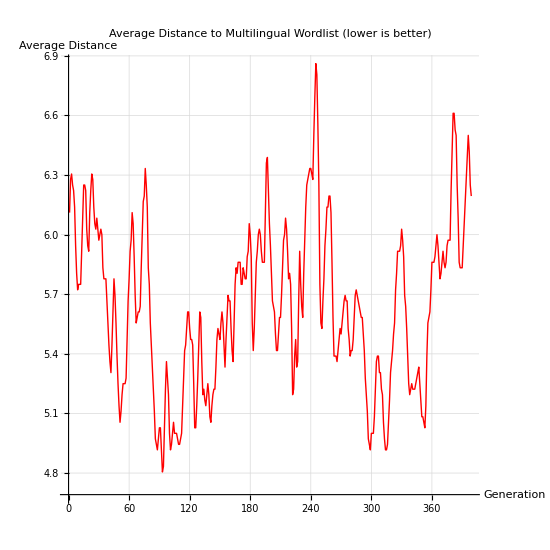

```mathematica
plotEvolutionProgress[baseWordStates, testList]
```

There is a weak decreasing trend in the average distance, showing a general improvement in evolution

## Generation with Neural Net Features

A more modern approach may be to take advantage of neural net embeddings. A neural net/deep learning model encodes words in a numeric representation called embeddings or feature vectors. For text, embeddings usually encode semantic meaning. We can ask the neural net to generate new words with similar embedding values as the training set (the original word list), generating new but similar words.

```mathematica
net=NetModel["Wolfram English Character-Level Language Model V1","TrainingNet"]
```

NetGraph[…]

```mathematica
vocabulary=Characters["\t\n !\"#$%&'()*+,-./0123456789:;<=>?@ABCDEFGHIJKLMNOPQRSTUVWXYZ[\\]^_`abcdefghijklmnopqrstuvwxyz{}é"];
```

```mathematica
net=NetReplacePart[net,"Input"->NetEncoder[{"Characters",{vocabulary,{StartOfString,EndOfString}->97}}]]
```

NetGraph[…]

```mathematica
results = 
 NetTrain[net, <|"Input" -> translatedList|>, All, LossFunction -> "Loss",   MaxTrainingRounds ->500]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:500  rounds:500  time:11s  examples/s:549
data | ,,  training examples:12  processed examples:6000  skipped examples:0
method | ,,  ADAMoptimizer  batch size12CPU
round | ,,  loss:3.58×10^-1  error:15.0%
 | 
 | ]

```mathematica
trainednet=results["TrainedNet"];
generator=NetReplacePart[NetExtract[trainednet,"predict"],{"Input"->NetEncoder[{"Characters",{vocabulary,EndOfString},"TargetLength"->1}],"Output"->NetDecoder[{"Class",Append[vocabulary,""]}]}]
```

NetChain[<3>]

```mathematica
wordz[]:=With[{obj=NetStateObject[generator]},StringJoin@NestWhileList[obj[Last[#],"RandomSample"]&,{"",""},#=!={""}&,SYLLABLECOUNT,SYLLABLECOUNT+2]];
```

```mathematica
newAvgWords=Sort@Complement[Table[wordz[],15],translatedList]
```

{baya,bkhy,caus,haqy,krpa,matt,schn,sred}

```mathematica
allPossibleWords = Flatten[Join[{newAvgWords,bestWordGeneticPool, mostDigramGenerated, mostFreqCharWord, bestWord}]]
```

{baya,bkhy,caus,haqy,krpa,matt,schn,sred,maaaq,me,meea,meeaan,meeaanan,mahaai,maya}

```mathematica
extractor=NetChain[{trainednet,AggregationLayer[Max,1]}]
```

NetChain[<2>]

```mathematica
a="tet"
b="det"
c="net"
```

tet

det

net

```mathematica
phoneticDifference[word1_String,word2_String]:=Module[{soundex1,soundex2},
soundex1=ResourceFunction["Soundex"][word1];
soundex2=ResourceFunction["Soundex"][word2];
Print["s1 ", soundex1];Print["s2 ", soundex2];
If[soundex1===soundex2,0,EditDistance[soundex1,soundex2]]]

(*Test function*)
testPhoneticDifference[word1_String,word2_String]:=Module[{diff},diff=phoneticDifference[word1,word2];
Print["\""<>word1<>"\" vs \""<>word2<>"\": "<>ToString[diff]];
diff]

(*Example usage*)
testPhoneticDifference["cat","kat"]
testPhoneticDifference["phone","fone"]
testPhoneticDifference["write","right"]
testPhoneticDifference["hello","halo"]
testPhoneticDifference["knight","night"]
```

## Ease of pronunciation

Now that we have a list of possibly generated words from our different methods,

```mathematica
allPossibleWords
```

{baya,bkhy,caus,haqy,krpa,matt,schn,sred,maaaq,me,meea,meeaan,meeaanan,mahaai,maya}

```mathematica
pronounceabilityScore[str_String]:=Module[{knownWords,syllables,vowelCount,consonantCount,vowelConsonantPenalty,dictionaryMatch,rareClusterPenalty,normalizedLength,totalScore},rareClusterPenalty=StringCount[str,RegularExpression["[^aeiouyAEIOUY]{3,}"]];
If[rareClusterPenalty>0,Return[1000]];
knownWords=DictionaryLookup["*"];
syllables=StringCount[ToLowerCase[str],RegularExpression["[aeiouy]+"]];
dictionaryMatch=Min[EditDistance[ToLowerCase[str],#]&/@Select[knownWords,Abs[StringLength[#]-StringLength[str]]<=2&]];
normalizedLength=StringLength[str]/10.0;
vowelCount=StringCount[str,RegularExpression["[aeiouyAEIOUY]"]];
consonantCount=StringLength[str]-vowelCount;
vowelConsonantPenalty=Abs[vowelCount-consonantCount]/StringLength[str];
totalScore=syllables+dictionaryMatch/10+vowelConsonantPenalty+normalizedLength;
totalScore;]
```

```mathematica
pronounceabilityScore[#]&/@allPossibleWords;
sortedByPronunciation = Reverse[SortBy[allPossibleWords,pronounceabilityScore]];
sortedByPronunciation
```

{sred,meeaanan,meeaan,meea,me,maya,matt,mahaai,maaaq,haqy,caus,baya,schn,krpa,bkhy}

## Evaluation and Visualization

```mathematica
allPossibleWords
```

{baya,bkhy,caus,haqy,krpa,matt,schn,sred,maaaq,me,meea,meeaan,meeaanan,mahaai,maya}

```mathematica
coordinatesAll=DimensionReduce[DeleteDuplicates[Join[allPossibleWords, translatedList]],2, FeatureExtractor->extractor, Method->"TSNE", PerformanceGoal->"Quality"];
coordinatesAll;
```

```mathematica
coordinatesBase=DimensionReduce[DeleteDuplicates[translatedList],2, FeatureExtractor->extractor, Method->"TSNE", PerformanceGoal->"Quality"];
coordinatesBase;
```

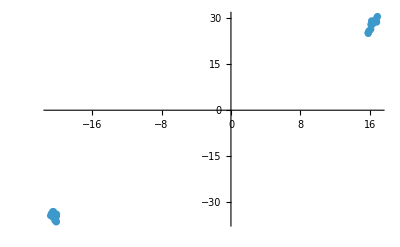

```mathematica
ListPlot[coordinatesAll]
```

```mathematica
coordinatesGen=DimensionReduce[DeleteDuplicates[allPossibleWords],2, FeatureExtractor->extractor, Method->"TSNE", PerformanceGoal->"Quality"];
coordinatesGen;
```

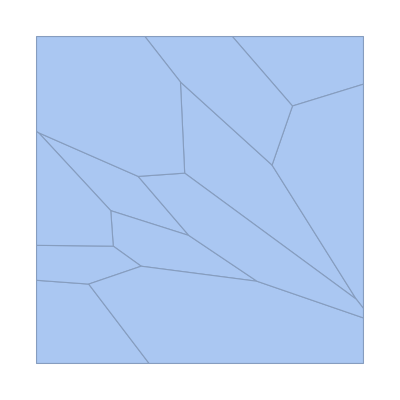

```mathematica
VoronoiMesh[coordinatesBase, AspectRatio->1]
```

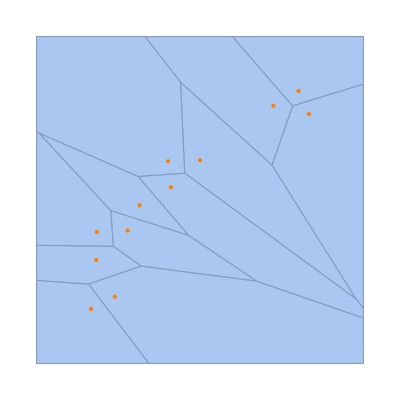

```mathematica
Show[%,Graphics[{Orange,Point[coordinatesBase]}, AspectRatio->1]]
```

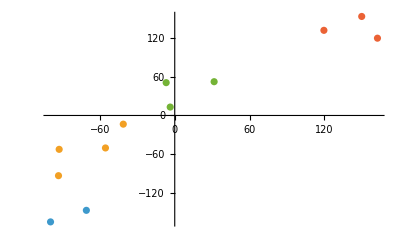

```mathematica
ListPlot[FindClusters[coordinatesBase,4,Method->"KMeans"]]
```

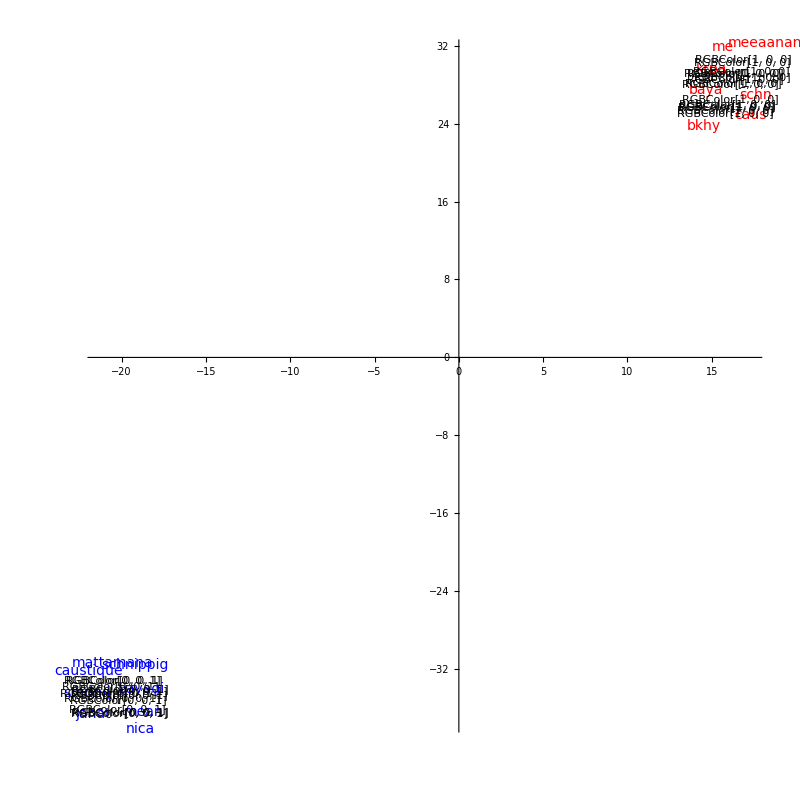

```mathematica
FeatureSpacePlot[
DeleteDuplicates[Join[
Labeled[#->Red, Style[#, Red, 14]]&/@allPossibleWords,
Labeled[#->Blue, Style[#, Blue, 14]]&/@translatedList
]],
FeatureExtractor->extractor,
LabelingSize->30,Axes->True, Method->"TSNE",ImageSize->{800,800}, AspectRatio->1
]
```

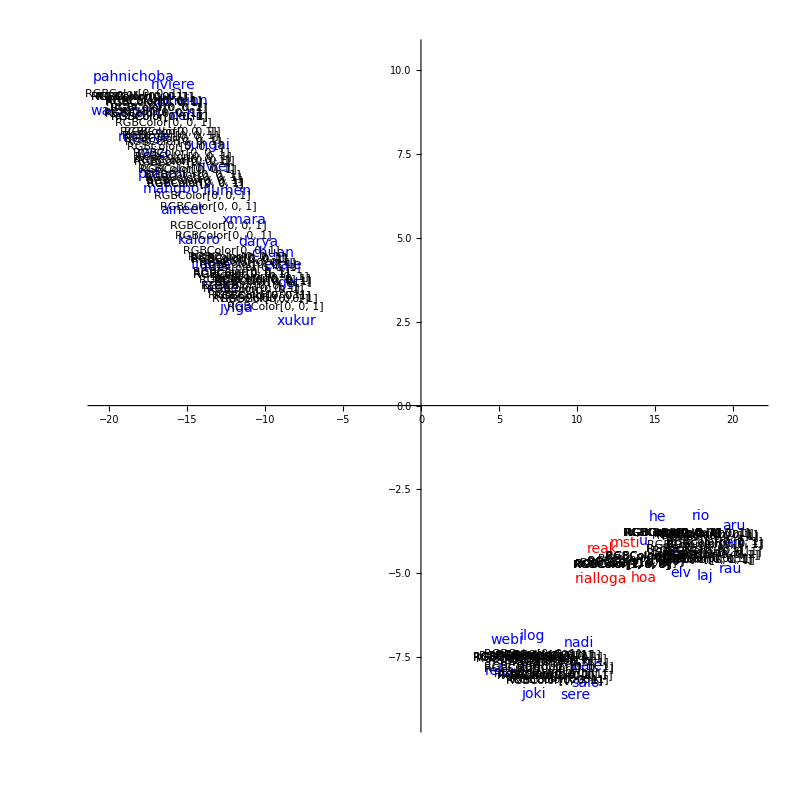

-Graphics-

## Metrics

We have some approaches which provide us with reasonable results. However, we need to quantify and visualize our newly generated words.

```mathematica
plotFitnessHeatmap[allPossibleWords]
```

plotFitnessHeatmap[{baya,bkhy,caus,haqy,krpa,matt,schn,sred,maaaq,me,meea,meeaan,meeaanan,mahaai,maya}]

```mathematica
WordCloud[StringTake[allPossibleWords, 1]]
```

-Graphics-

```mathematica
plotFitnessHeatmap[allPossibleWords_List]:=Module[{fitnessValues,reshapedValues,size,wordsMatrix},
	  fitnessValues=extractor /@ allPossibleWords;
	  size=Ceiling[Sqrt[Length[fitnessValues]]];
	  reshapedValues=PadRight[Partition[fitnessValues,size,size,{1,1},{}],{size,sh`ize},None];
	  wordsMatrix=PadRight[Partition[allPossibleWords,size,size,{1,1},""],{size,size},None];
	  S 33
	]
```

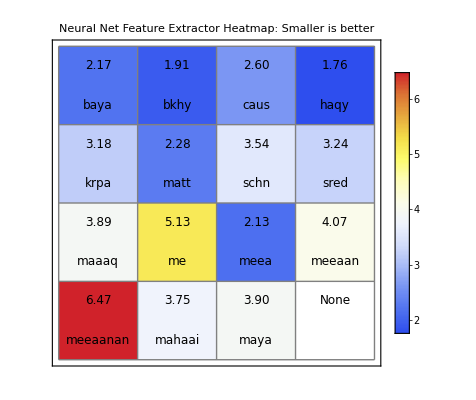

```mathematica
plotFitnessHeatmap[allPossibleWords]
```